# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Left Handed Decay width - SM , dim 6 interference - 1404 / 4 /10 )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

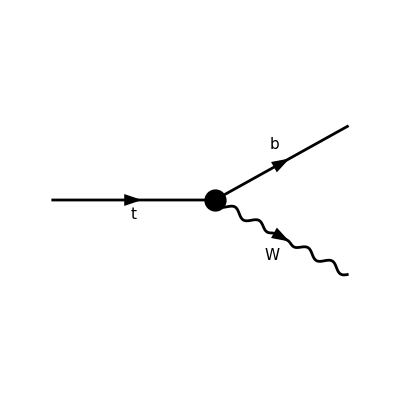

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

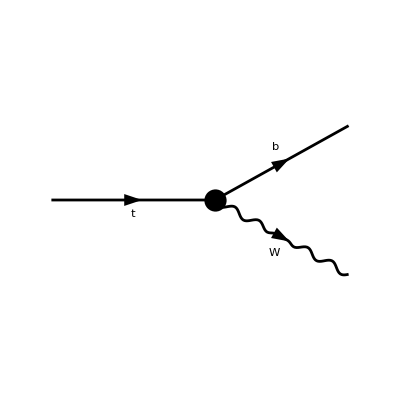

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+

```mathematica
(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+
```

4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-

```mathematica
4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-
```

2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+

```mathematica
2 Sqrt[2] g MinkSP[pt,Eplh] MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2
+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+
```

4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+

```mathematica
4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]*MinkSP[pt,pW]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]*MinkSP[pt,pW]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]*MinkSP[pt,pW]+MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-I ((LeviCivitaContraction[pb,pt,Epclh,Eplh]-I (MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]))*MinkSP[pW,pW]-LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]+LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh])+(MinkSP[pb,pt]*MinkSP[pW,pW]-2 MinkSP[pb,pW]*MinkSP[pt,pW])*MinkSP[Epclh,Eplh]))+
```

(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+

```mathematica
Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^4+
```

128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+

```mathematica
128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+
```

32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-

```mathematica
32 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh]-32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[pb,pW] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D]-
```

ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+

```mathematica
I LeviCivitaContraction[pb,pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[pb,pW,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+
```

4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+

```mathematica
4 C3q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[pb,Eplh]*(MinkSP[pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Epclh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+
```

(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
MinkSP[pb,Epclh]*(MinkSP[pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Eplh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))
```

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
Epl=1/(mw){pw,-EW Sin[θ]Cos[ϕ],-EW Sin[θ] Sin[ϕ],-EW Cos[θ]};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt0=(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[Pb,Pt,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]-MinkSP[Pb,Pt]*MinkSP[Epl,Epl])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[Pb,Pt,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]-MinkSP[Pb,Pt]*MinkSP[Epl,Epl])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[Pb,Pw,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pb,Pw]*MinkSP[Epl,Epl])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epl,Epl]+I (MinkSP[Pt,Epl]*MinkSP[Pw,Epl]+MinkSP[Pt,Epl]*MinkSP[Pw,Epl]))+MinkSP[Epl,Epl]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[Pt,Pw]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epl,Epl]+I (MinkSP[Pt,Epl]*MinkSP[Pw,Epl]+MinkSP[Pt,Epl]*MinkSP[Pw,Epl]))+MinkSP[Epl,Epl]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epl]*MinkSP[Pw,Epl]-MinkSP[Pw,Pw]*MinkSP[Epl,Epl])-4 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epl,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[Pt,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pt,Pw]*MinkSP[Epl,Epl])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g MinkSP[Pt,Epl] MinkSP[Pw,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epl]*MinkSP[Pw,Epl]-MinkSP[Pw,Pw]*MinkSP[Epl,Epl])-2 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epl,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[Pt,Epl]*MinkSP[Pw,Epl]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[Pt,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pt,Pw]*MinkSP[Epl,Epl])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[Pb,Pt,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]-MinkSP[Pb,Pt]*MinkSP[Epl,Epl])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[Pb,Pw,Epl,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]-2 MinkSP[Pb,Pw]*MinkSP[Epl,Epl])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[Pb,Pw,Epl,Epl]*MinkSP[Pt,Pw]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]*MinkSP[Pt,Pw]+MinkSP[Pb,Epl]*MinkSP[Pw,Epl]*MinkSP[Pt,Pw]+MinkSP[Pb,Pw]*MinkSP[Pt,Epl]*MinkSP[Pw,Epl]+MinkSP[Pb,Pw]*MinkSP[Pt,Epl]*MinkSP[Pw,Epl]-MinkSP[Pb,Pt]*MinkSP[Pw,Epl]*MinkSP[Pw,Epl]-I ((LeviCivitaContraction[Pb,Pt,Epl,Epl]-I (MinkSP[Pb,Epl]*MinkSP[Pt,Epl]+MinkSP[Pb,Epl]*MinkSP[Pt,Epl]))*MinkSP[Pw,Pw]-LeviCivitaContraction[Pb,Pt,Pw,Epl]*MinkSP[Pw,Epl]+LeviCivitaContraction[Pb,Pt,Pw,Epl]*MinkSP[Pw,Epl])+(MinkSP[Pb,Pt]*MinkSP[Pw,Pw]-2 MinkSP[Pb,Pw]*MinkSP[Pt,Pw])*MinkSP[Epl,Epl]))+Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^4-128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Epl] MinkSP[Pw,Epl] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^4-256 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epl,Epl] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epl,Epl] Lambda^4-32 g^2 vev^4 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Epl] MinkSP[Pw,Epl] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epl,Epl] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epl,Epl] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epl,Epl] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Re[C2q2H4D] Lambda^2+32 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epl] MinkSP[Pw,Epl]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epl] MinkSP[Pw,Epl]-32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Epl] MinkSP[Pw,Epl]+4 C2q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-3 C3q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epl,Epl]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[Pb,Pw] MinkSP[Epl,Epl]-64 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epl,Epl]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epl,Epl]-16 C2q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[Pb,Pw] MinkSP[Epl,Epl] Re[C2q2H4D]-I LeviCivitaContraction[Pb,Pt,Epl,Epl]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[Pb,Pw,Epl,Epl]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+4 C3q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epl,Epl] Re[C3q2H4D]+MinkSP[Pb,Epl]*(MinkSP[Pt,Epl]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epl]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+MinkSP[Pb,Epl]*(MinkSP[Pt,Epl]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epl]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8 mw^2)mt Nc (32 Eb (EW^2-pb pw)^2 vev^6 Conjugate[C1qdWH3]^2+128 Eb Lambda^4 (EW^2-pb pw)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 (2 EW pb pw+Eb (EW^2+pw^2)) vev^4 Conjugate[CHud]^2+4 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (-g (2 EW pb pw+Eb (EW^2+pw^2)) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 √2 EW^3 vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 √2 EW pb pw vev (2 CtW Lambda^2+C1quWH3 vev^2)+EW^2 g (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)-g pw^2 (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g (EW-pw) (EW+pw) vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+32 Lambda^2 (EW^2-pb pw) vev Conjugate[CbW] (-4 mb (EW^2-pb pw) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb EW+pb pw) vev^2 Conjugate[CHud]+(Eb EW+pb pw) vev^4 Conjugate[CudH4D]-EW mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 (EW^2-pb pw) vev^3 Conjugate[C1qdWH3] (8 Eb Lambda^2 (EW^2-pb pw) vev Conjugate[CbW]-4 mb (EW^2-pb pw) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (Eb EW+pb pw) vev^2 Conjugate[CHud]+(Eb EW+pb pw) vev^4 Conjugate[CudH4D]-EW mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 √2 EW^3 vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 √2 EW pb pw vev (2 CtW Lambda^2+C1quWH3 vev^2)+EW^2 g (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)-g pw^2 (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g (EW-pw) (EW+pw) vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 (2 EW pb pw+Eb (EW^2+pw^2))+64 √2 CtW g Lambda^6 (EW^2-pb pw) (Eb EW+pb pw) vev+4 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 (EW^2-pb pw) (Eb EW+pb pw) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+8 g^2 (2 EW pb pw+Eb (EW^2+pw^2)) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 Eb (EW^2-pb pw)^2+g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3phiq])+8 vev^6 (4 C1quWH3^2 Eb (EW^2-pb pw)^2+2 g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 (EW^2-pb pw) (Eb EW+pb pw) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW Eb (EW^2-pb pw)^2+g^2 Lambda^2 (2 EW pb pw+Eb (EW^2+pw^2)) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW^2-pb pw) (Eb EW+pb pw) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (4 C2q2H4D^2 (2 EW pb pw+Eb (EW^2+pw^2))+C3q2H4D^2 (6 EW pb pw+Eb (EW^2+pw^2))-2 C3q2H4D Eb (EW^2+pw^2) Conjugate[C3q2H4D]+(2 EW pb pw+Eb (EW^2+pw^2)) Conjugate[C3q2H4D]^2+8 Re[C2q2H4D] (2 ⅈ Eb (EW^2+pw^2) Im[C3q2H4D]+4 EW pb pw (C3q2H4D-Re[C3q2H4D]))-8 C3q2H4D EW pb pw Re[C3q2H4D])))

```mathematica
(*Total Decay Width*)
```

```mathematica
Msqtot=(1/(32 Lambda^8 MinkSP[Pw,Pw])) Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^4-8 g Lambda^2 Conjugate[CHud] (3 MinkSP[Pw,Pw] (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D] (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) vev^2-24 mb Conjugate[CKM3x3] MinkSP[Pw,Pw] (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 MinkSP[Pw,Pw] (MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))+(Conjugate[CKM3x3])^2 (MinkSP[Pb,Pt] MinkSP[Pw,Pw] (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw] (MinkSP[Pt,Pw] (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

1/(32 Lambda^8 (EW-pb) (EW+pb))Nc (4 g^2 Lambda^4 mt (3 Eb EW^2-(Eb-2 EW) pb^2) vev^4 Conjugate[CHud]^2+4 mt (8 (EW-pb) (EW+pb) (3 Eb EW^2+(Eb+4 EW) pb^2) (vev^3 Conjugate[C1qdWH3]+2 Lambda^2 vev Conjugate[CbW])^2+12 √2 g (EW-pb) (EW+pb) (Eb EW+pb^2) vev^5 (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) Conjugate[CudH4D]+g^2 (3 Eb EW^2-(Eb-2 EW) pb^2) vev^8 Conjugate[CudH4D]^2)-8 g Lambda^2 vev^2 Conjugate[CHud] (g mt (-2 EW pb^2+Eb (-3 EW^2+pb^2)) vev^4 Conjugate[CudH4D]+3 (EW-pb) (EW+pb) (-2 √2 mt (Eb EW+pb^2) vev (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])+mb mt Conjugate[CKM3x3] (2 √2 EW vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))-24 mb (EW-pb) (EW+pb) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (2 √2 EW vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (4 mt (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 EW g mt (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (2 mt (Eb EW+pb^2) (64 EW (EW-pb) (EW+pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2+24 √2 g (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+EW g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+Eb mt (EW-pb) (EW+pb) (-32 (EW-pb) (EW+pb) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2+g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)+g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
(*Eb=mt-EW;*)
pw=pb;
(*pb=(1/(2 mt)) Sqrt[mt^2 - (mb + mw)^2] Sqrt[mt^2 - (mb - mw)^2];*)
```

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidth0=Integrate[Msqt0 *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(1024 Lambda^8 mt^3 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (32 mw^4 (mb^2+mt^2-mw^2) vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 mw^4 (mb^2+mt^2-mw^2) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^4 Conjugate[CHud]^2+4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev^4 Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mw^2 (mb^2+mt^2-mw^2) vev Conjugate[CbW]-8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-32 Lambda^2 mw^2 vev Conjugate[CbW] (8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mw^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-Conjugate[CKM3x3]^2 (-16 g^2 Lambda^8 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)+64 √2 CtW g Lambda^6 mt mw^2 (mb^2-mt^2+mw^2) vev-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])-8 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])-32 Lambda^4 vev^2 (4 CtW^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq])-16 vev^6 (2 C1quWH3^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^2 vev^4 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (-((4 C2q2H4D^2+3 C3q2H4D^2) (mb^2-mt^2)^2)+(4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2) mw^2-2 C3q2H4D (mb^2+mt^2) mw^2 Conjugate[C3q2H4D]+(-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) Conjugate[C3q2H4D]^2-16 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Re[C2q2H4D] (C3q2H4D-Re[C3q2H4D])+4 C3q2H4D (mb^2-mt^2)^2 Re[C3q2H4D])))

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthtotal=Integrate[Msqtot*dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
DecayWidth0SM=DecayWidth0/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √((mb+mt-mw) (-mb+mt+mw)) ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
(* SM limit *)
```

```mathematica
DecayWidthtotalSM=DecayWidthtotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
F0=DecayWidth0/DecayWidthtotal//FullSimplify
```

(4 mt^4 (32 mw^4 (mb^2+mt^2-mw^2) vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 mw^4 (mb^2+mt^2-mw^2) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^4 Conjugate[CHud]^2+4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev^4 Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mw^2 (mb^2+mt^2-mw^2) vev Conjugate[CbW]-8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-32 Lambda^2 mw^2 vev Conjugate[CbW] (8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mw^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-Conjugate[CKM3x3]^2 (-16 g^2 Lambda^8 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)+64 √2 CtW g Lambda^6 mt mw^2 (mb^2-mt^2+mw^2) vev-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])-8 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])-32 Lambda^4 vev^2 (4 CtW^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq])-16 vev^6 (2 C1quWH3^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^2 vev^4 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (-((4 C2q2H4D^2+3 C3q2H4D^2) (mb^2-mt^2)^2)+(4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2) mw^2-2 C3q2H4D (mb^2+mt^2) mw^2 Conjugate[C3q2H4D]+(-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) Conjugate[C3q2H4D]^2-16 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Re[C2q2H4D] (C3q2H4D-Re[C3q2H4D])+4 C3q2H4D (mb^2-mt^2)^2 Re[C3q2H4D]))))/(16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
(* SM Limit*)
```

```mathematica
F0SM=DecayWidth0SM/DecayWidthtotalSM//FullSimplify
```

((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
Clear[Lambda,sw,e,vev,g,mb,mt, mw,CKM3x3]
```

```mathematica
(*Define parameters and constants based on PHYSICAL REVIEW D 100,056023 (2019)*)
Lambda=500;e=0.31345;vev=246;g=0.6483;mb=4.78;mt=173.0; mw=80.379;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq;
C1quWH3;
C1qdWH3;
C2q2H4D;
C3q2H4D;
CudH4D;
```

```mathematica
F0
```

(3.58298×10^9 (1.5389×10^12 Conjugate[C1qdWH3] (-1.05144×10^10 (60516 C1quWH3+85000.)-0.916835 (173834. (3662186256 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+30258000000 Conjugate[C3phiq]+3662186256 C3q2H4D+125000000000)-1.4854×10^16 Conjugate[CudH4D]-7.87913×10^17)+1.54569×10^17)+6.95398×10^27 (Conjugate[C1qdWH3])^2+3545933815489536 (1.96112×10^12 C1quWH3^2+7.36422×10^13 Conjugate[C3phiq] (C2q2H4D-Re(C3q2H4D)+C3q2H4D))-1.00749×10^12 (61765.1 (1.26519×10^7 (60516 C1quWH3+85000.)+6.78723×10^6 (60516 (Conjugate[C2q2H4D]-Re(C3q2H4D))+500000 Conjugate[C3phiq])+112.156 (3662186256 (C2q2H4D+C3q2H4D)+125000000000))-1.66399×10^18 Conjugate[CudH4D])-2.63197×10^13 (1.05144×10^10 (60516 C1quWH3+85000.)+0.916835 (173834. (3662186256 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+30258000000 Conjugate[C3phiq]+3662186256 C3q2H4D+125000000000)-1.4854×10^16 Conjugate[CudH4D]-7.87913×10^17))-1.17314×10^15 Conjugate[CudH4D] (1.26519×10^7 (60516 C1quWH3+85000.)+6.78723×10^6 (60516 (Conjugate[C2q2H4D]-Re(C3q2H4D))+500000 Conjugate[C3phiq])+112.156 (3662186256 (C2q2H4D+C3q2H4D)+125000000000))+1.73159×10^29 (C1quWH3 Conjugate[C3phiq]+0.17 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D))+14648745024000000 (1.33356×10^12 C1quWH3+7.36422×10^13 (Conjugate[C2q2H4D]+C2q2H4D+(Conjugate[C3phiq])^2-Re(C3q2H4D)+C3q2H4D))+2.09578×10^28 C1quWH3 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+7.15344×10^29 (C1quWH3+0.34 Conjugate[C3phiq])-5.6368×10^18 (1.93512×10^8 (4 C2q2H4D^2+C3q2H4D^2)-8.94378×10^8 (4 C2q2H4D^2+3 C3q2H4D^2)-1.12138×10^10 Re(C2q2H4D) (C3q2H4D-Re(C3q2H4D))-7.00865×10^8 (Conjugate[C3q2H4D])^2-3.87025×10^8 C3q2H4D Conjugate[C3q2H4D]+3.57751×10^9 C3q2H4D Re(C3q2H4D))+5.22261×10^23 Conjugate[C2q2H4D] (60516 C2q2H4D+500000 Conjugate[C3phiq])+1.58026×10^28 (Conjugate[C2q2H4D])^2+121032000000000000 (7.36422×10^13 Conjugate[C3phiq]+1.13352×10^11)+1.58026×10^28 (Conjugate[CudH4D])^2+6.59123×10^31))/(-3.60982×10^21 (-3.31024×10^18 Conjugate[C1qdWH3]+185295. (1.26519×10^7 (60516 C1quWH3+85000.)+6.78723×10^6 (60516 (Conjugate[C2q2H4D]-Re(C3q2H4D))+500000 Conjugate[C3phiq])+112.156 (3662186256 (C2q2H4D+C3q2H4D)+125000000000))-2.38466×10^18 Conjugate[CudH4D]-5.66148×10^19)+7.55245×10^15 (1.66966×10^9 Conjugate[CudH4D] (-1.26519×10^7 (60516 C1quWH3+85000.)-112.156 (3662186256 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+3662186256 C3q2H4D+125000000000)-3.39361×10^12 Conjugate[C3phiq])-173. (60516 Conjugate[C1qdWH3]+1.035×10^6) (2.19966×10^9 (60516 C1quWH3+85000.)+33342.5 (3662186256 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+30258000000 Conjugate[C3phiq]+3662186256 C3q2H4D+125000000000)))+8.67311×10^14 (-1.56392×10^9 Conjugate[C1qdWH3] (-1.66081×10^14 Conjugate[CudH4D]-6.4315×10^15)+2.94054×10^23 (Conjugate[C1qdWH3])^2+9.35562×10^22 (Conjugate[CudH4D])^2+4.44228×10^24 Conjugate[CudH4D]+8.60137×10^25)-8.40043×10^13 (-1.21004×10^10 (60516 C1quWH3+85000.) (3662186256 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+30258000000 Conjugate[C3phiq]+3662186256 C3q2H4D+125000000000)-9.10001×10^14 (60516 C1quWH3+85000.)^2-15284.8 (13411608173635297536 (4 C2q2H4D^2+C3q2H4D^2)+121032000000 Conjugate[C3phiq] (7324372512 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+250000000000)+13411608173635297536 (16 ⅈ Re(C2q2H4D) Im(C3q2H4D)+(Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D])+3662186256000000000000 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+53646432694541190144 (Conjugate[C2q2H4D])^2+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+3662186256000000000000 (Conjugate[C3phiq])^2+62500000000000000000000))-5.43791×10^17 (1.25114×10^10 (60516 C1quWH3+85000.)^2-0.420293 (13411608173635297536 (4 C2q2H4D^2+C3q2H4D^2)+3662186256000000000000 (C2q2H4D+C3q2H4D)+62500000000000000000000)-25434.4 (2000000 Conjugate[C3phiq] (7324372512 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+250000000000)+3545933815489536 ⅈ Re(C2q2H4D) Im(C3q2H4D)+886483453872384 (Conjugate[C2q2H4D])^2+484128 (3662186256 C2q2H4D+125000000000) Conjugate[C2q2H4D]+60516000000000000 (Conjugate[C3phiq])^2+221620863468096 (Conjugate[C3q2H4D])^2-443241726936192 C3q2H4D Conjugate[C3q2H4D]-60516000000000000 Re(C3q2H4D)))+2.28306×10^41)

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
F0
```

0.500741

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
Table[{C1quWH3,F0-F0SM},{C1quWH3,-1,1,0.2}]
```

(-1. | -0.194747
-0.8 | -0.195184
-0.6 | -0.195633
-0.4 | -0.196094
-0.2 | -0.196566
0. | -0.197049
0.2 | -0.197544
0.4 | -0.198049
0.6 | -0.198566
0.8 | -0.199094
1. | -0.199632)

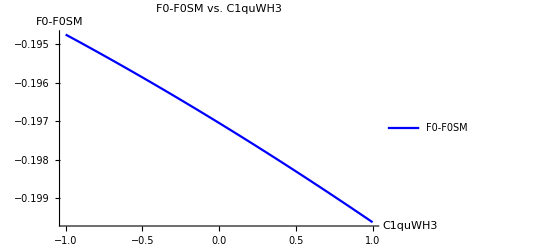

```mathematica
Plot[F0-F0SM,{C1quWH3,-1,1},PlotStyle->{Blue},AxesLabel->{"C1quWH3 ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

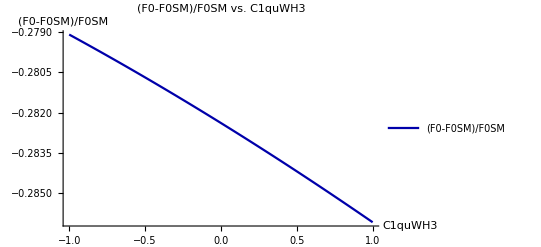

```mathematica
Plot[(F0-F0SM)/F0SM,{C1quWH3,-1,1},PlotStyle->{Darker[Blue]},AxesLabel->{"C1quWH3 ","(F0-F0SM)/F0SM"},PlotLabel->"(F0-F0SM)/F0SM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"(F0-F0SM)/F0SM"}]
```

```mathematica
F0
```

(3.58298×10^9 (3545933815489536 (1.96112×10^12 C1quWH3^2+0.)+7.15344×10^29 (C1quWH3+0.)+14648745024000000 (1.33356×10^12 C1quWH3+0.)-2.63197×10^13 (1.05144×10^10 (60516 C1quWH3+85000.)-7.02464×10^17)-1.00749×10^12 (61765.1 (1.26519×10^7 (60516 C1quWH3+85000.)+1.40195×10^13)+0.)+6.5926×10^31))/(7.55245×10^15 (0.-1.79055×10^8 (2.19966×10^9 (60516 C1quWH3+85000.)+4.16781×10^15))-8.40043×10^13 (-9.10001×10^14 (60516 C1quWH3+85000.)^2-1.51255×10^21 (60516 C1quWH3+85000.)-9.55298×10^26)-5.43791×10^17 (1.25114×10^10 (60516 C1quWH3+85000.)^2-2.62683×10^22)-3.60982×10^21 (185295. (1.26519×10^7 (60516 C1quWH3+85000.)+1.40195×10^13)-5.66148×10^19)+3.02906×10^41)

```mathematica
(* Chi Squared*)
```

```mathematica
(*داده‌های آزمایشی- F0=0.681±0.012 (stat)±0.023 (syst), Sqrt[s]= 8Tev  *)
F0exp=0.687;dF0=0.018;
```

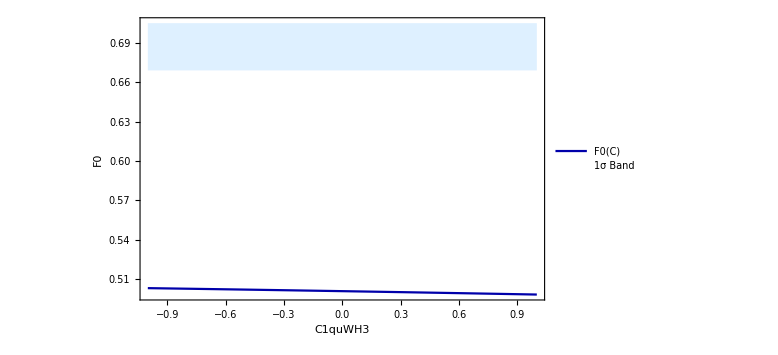

```mathematica
Plot[{F0,F0exp-dF0,F0exp+dF0},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C1quWH3","F0"},PlotLegends->{"F0(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

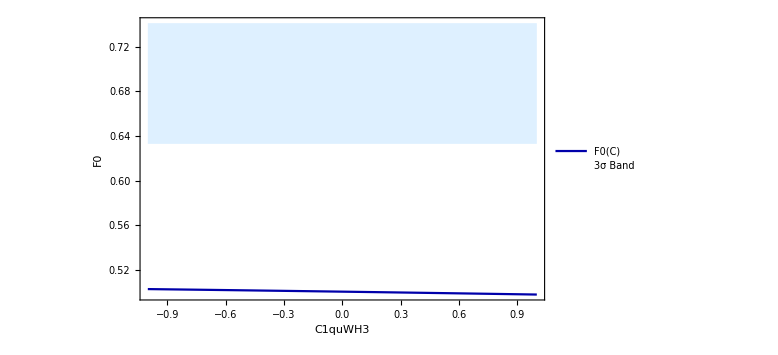

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C1quWH3","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
Table[{C1qdWH3,F0-F0SM},{C1qdWH3,-1,1,0.2}]
```

(-1. | -0.187767
-0.8 | -0.189646
-0.6 | -0.191514
-0.4 | -0.19337
-0.2 | -0.195215
0. | -0.197049
0.2 | -0.198872
0.4 | -0.200684
0.6 | -0.202484
0.8 | -0.204274
1. | -0.206053)

```mathematica
F0
```

(3.58298×10^9 (6.95398×10^27 (Conjugate[C1qdWH3])^2+1.31751×10^30 Conjugate[C1qdWH3]+8.34518×10^31))/(7.55245×10^15 (0.-7.53377×10^17 (60516 Conjugate[C1qdWH3]+1.035×10^6))-3.60982×10^21 (-3.31024×10^18 Conjugate[C1qdWH3]-5.38178×10^19)+8.67311×10^14 (2.94054×10^23 (Conjugate[C1qdWH3])^2+1.00584×10^25 Conjugate[C1qdWH3]+8.60137×10^25)+3.34142×10^41)

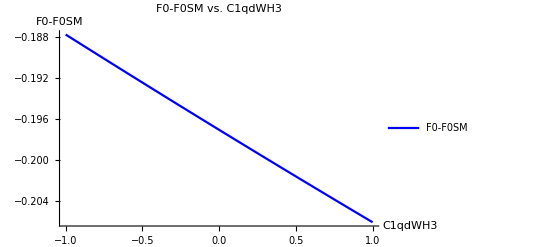

```mathematica
Plot[F0-F0SM,{C1qdWH3,-1,1},PlotStyle->{Blue},AxesLabel->{"C1qdWH3 ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C1qdWH3 ",PlotRange->All,
PlotLegends->{"F0-F0SM"}]
```

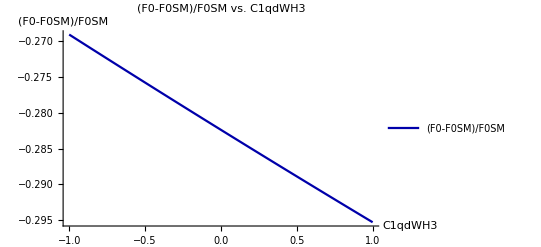

```mathematica
Plot[(F0-F0SM)/F0SM,{C1qdWH3,-1,1},PlotStyle->{Darker[Blue]},AxesLabel->{"C1qdWH3 ","(F0-F0SM)/F0SM"},PlotLabel->"(F0-F0SM)/F0SM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"(F0-F0SM)/F0SM"}]
```

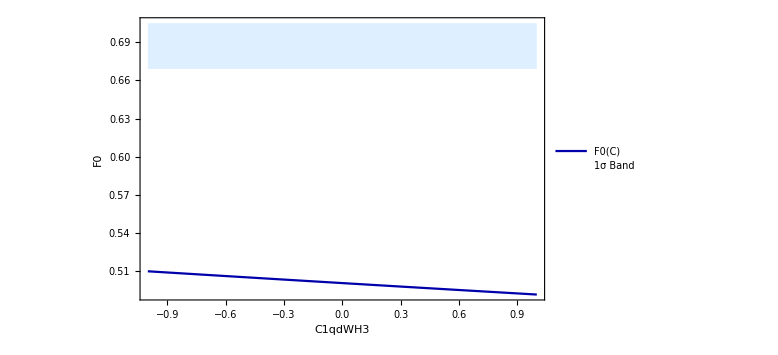

```mathematica
Plot[{F0,F0exp-dF0,F0exp+dF0},{C1qdWH3,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C1qdWH3","F0"},PlotLegends->{"F0(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1qdWH3","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

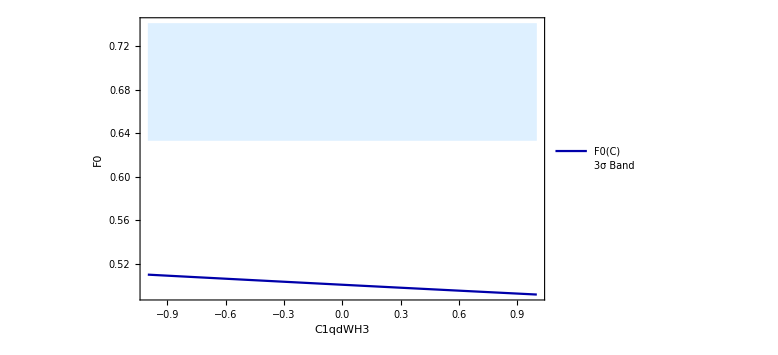

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{C1qdWH3,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C1qdWH3","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1qdWH3","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
Table[{C2q2H4D,F0-F0SM},{C2q2H4D,-1,1,0.2}]
```

(-1. | -0.200732+0. ⅈ
-0.8 | -0.200002+0. ⅈ
-0.6 | -0.199269+0. ⅈ
-0.4 | -0.198533+0. ⅈ
-0.2 | -0.197792+0. ⅈ
0. | -0.197049+0. ⅈ
0.2 | -0.196303+0. ⅈ
0.4 | -0.195553+0. ⅈ
0.6 | -0.1948+0. ⅈ
0.8 | -0.194045+0. ⅈ
1. | -0.193287+0. ⅈ)

```mathematica
F0
```

(3.58298×10^9 (-5.6368×10^18 (0.-2.80346×10^9 C2q2H4D^2)+1.58026×10^28 (Conjugate[C2q2H4D])^2+3.16051×10^28 C2q2H4D Conjugate[C2q2H4D]+2.9437×10^28 (Conjugate[C2q2H4D]+C2q2H4D)+14648745024000000 (7.36422×10^13 (Conjugate[C2q2H4D]+C2q2H4D)+0.)-1.00749×10^12 (61765.1 (4.10736×10^11 Conjugate[C2q2H4D]+112.156 (3662186256 C2q2H4D+125000000000)+1.07541×10^12)+0.)-2.63197×10^13 (0.916835 (173834. (3662186256 (Conjugate[C2q2H4D]+C2q2H4D)+125000000000)-7.87913×10^17)+8.93724×10^14)+6.5926×10^31))/(7.55245×10^15 (0.-1.79055×10^8 (33342.5 (3662186256 (Conjugate[C2q2H4D]+C2q2H4D)+125000000000)+1.86971×10^14))-5.43791×10^17 (-0.420293 (53646432694541190144 C2q2H4D^2+3662186256000000000000 C2q2H4D+62500000000000000000000)-25434.4 (886483453872384 (Conjugate[C2q2H4D])^2+484128 (3662186256 C2q2H4D+125000000000) Conjugate[C2q2H4D])+9.03948×10^19)-8.40043×10^13 (-15284.8 (53646432694541190144 C2q2H4D^2+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+53646432694541190144 (Conjugate[C2q2H4D])^2+3662186256000000000000 (Conjugate[C2q2H4D]+C2q2H4D)+62500000000000000000000)-1.02853×10^15 (3662186256 (Conjugate[C2q2H4D]+C2q2H4D)+125000000000)-6.57476×10^24)-3.60982×10^21 (185295. (4.10736×10^11 Conjugate[C2q2H4D]+112.156 (3662186256 C2q2H4D+125000000000)+1.07541×10^12)-5.66148×10^19)+3.02906×10^41)

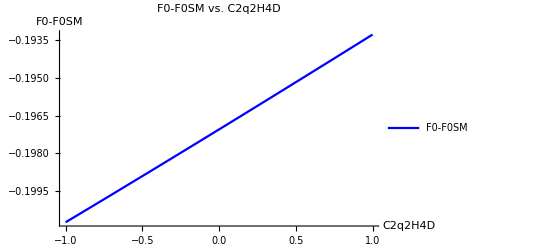

```mathematica
Plot[F0-F0SM,{C2q2H4D,-1,1},PlotStyle->{Blue},AxesLabel->{"C2q2H4D ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

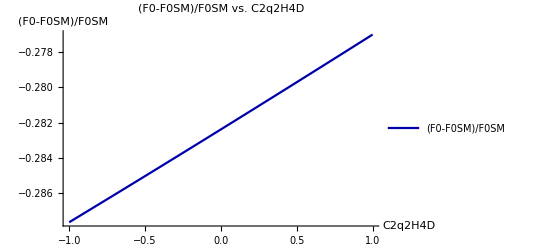

```mathematica
Plot[(F0-F0SM)/F0SM,{C2q2H4D,-1,1},PlotStyle->{Darker[Blue]},AxesLabel->{"C2q2H4D ","(F0-F0SM)/F0SM"},PlotLabel->"(F0-F0SM)/F0SM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"(F0-F0SM)/F0SM"}]
```

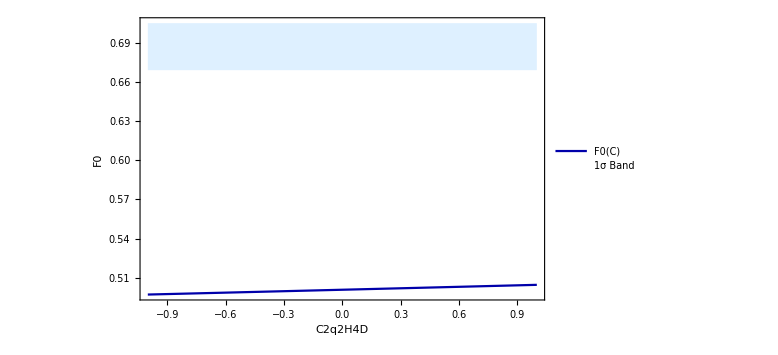

```mathematica
Plot[{F0,F0exp-dF0,F0exp+dF0},{C2q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C2q2H4D","F0"},PlotLegends->{"F0(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C2q2H4D","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
Table[{C3q2H4D,F0-F0SM},{C3q2H4D,-1,1,0.2}]
```

(-1. | -0.197049
-0.8 | -0.197049
-0.6 | -0.197049
-0.4 | -0.197049
-0.2 | -0.197049
0. | -0.197049
0.2 | -0.197049
0.4 | -0.197049
0.6 | -0.197049
0.8 | -0.197049
1. | -0.197049)

```mathematica
F0
```

(3.58298×10^9 (-5.6368×10^18 (-2.48962×10^9 C3q2H4D^2-3.87025×10^8 C3q2H4D Conjugate[C3q2H4D]-7.00865×10^8 (Conjugate[C3q2H4D])^2+3.57751×10^9 C3q2H4D Re(C3q2H4D)+0.)-2.63197×10^13 (0.916835 (173834. (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)-7.87913×10^17)+8.93724×10^14)-1.00749×10^12 (61765.1 (-4.10736×10^11 Re(C3q2H4D)+112.156 (3662186256 C3q2H4D+125000000000)+1.07541×10^12)+0.)+14648745024000000 (7.36422×10^13 (C3q2H4D-Re(C3q2H4D))+0.)+2.9437×10^28 (C3q2H4D-Re(C3q2H4D))+6.5926×10^31))/(7.55245×10^15 (0.-1.79055×10^8 (33342.5 (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)+1.86971×10^14))-5.43791×10^17 (-0.420293 (13411608173635297536 C3q2H4D^2+3662186256000000000000 C3q2H4D+62500000000000000000000)-25434.4 (221620863468096 (Conjugate[C3q2H4D])^2-443241726936192 C3q2H4D Conjugate[C3q2H4D]-60516000000000000 Re(C3q2H4D))+9.03948×10^19)-8.40043×10^13 (-15284.8 (13411608173635297536 C3q2H4D^2+13411608173635297536 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D])+3662186256000000000000 (C3q2H4D-Re(C3q2H4D))+62500000000000000000000)-1.02853×10^15 (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)-6.57476×10^24)-3.60982×10^21 (185295. (-4.10736×10^11 Re(C3q2H4D)+112.156 (3662186256 C3q2H4D+125000000000)+1.07541×10^12)-5.66148×10^19)+3.02906×10^41)

```mathematica
F0-F0SM
```

(3.58298×10^9 (-5.6368×10^18 (-2.48962×10^9 C3q2H4D^2-3.87025×10^8 C3q2H4D Conjugate[C3q2H4D]-7.00865×10^8 (Conjugate[C3q2H4D])^2+3.57751×10^9 C3q2H4D Re(C3q2H4D)+0.)-2.63197×10^13 (0.916835 (173834. (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)-7.87913×10^17)+8.93724×10^14)-1.00749×10^12 (61765.1 (-4.10736×10^11 Re(C3q2H4D)+112.156 (3662186256 C3q2H4D+125000000000)+1.07541×10^12)+0.)+14648745024000000 (7.36422×10^13 (C3q2H4D-Re(C3q2H4D))+0.)+2.9437×10^28 (C3q2H4D-Re(C3q2H4D))+6.5926×10^31))/(7.55245×10^15 (0.-1.79055×10^8 (33342.5 (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)+1.86971×10^14))-5.43791×10^17 (-0.420293 (13411608173635297536 C3q2H4D^2+3662186256000000000000 C3q2H4D+62500000000000000000000)-25434.4 (221620863468096 (Conjugate[C3q2H4D])^2-443241726936192 C3q2H4D Conjugate[C3q2H4D]-60516000000000000 Re(C3q2H4D))+9.03948×10^19)-8.40043×10^13 (-15284.8 (13411608173635297536 C3q2H4D^2+13411608173635297536 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D])+3662186256000000000000 (C3q2H4D-Re(C3q2H4D))+62500000000000000000000)-1.02853×10^15 (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)-6.57476×10^24)-3.60982×10^21 (185295. (-4.10736×10^11 Re(C3q2H4D)+112.156 (3662186256 C3q2H4D+125000000000)+1.07541×10^12)-5.66148×10^19)+3.02906×10^41)-0.69779

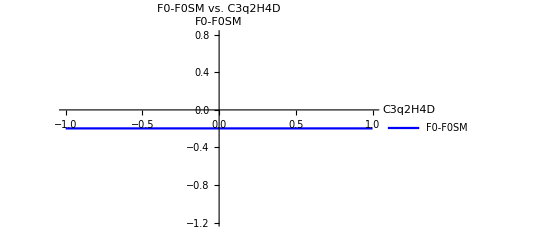

```mathematica
Plot[F0-F0SM,{C3q2H4D,-1,1},PlotStyle->{Blue},AxesLabel->{"C3q2H4D ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

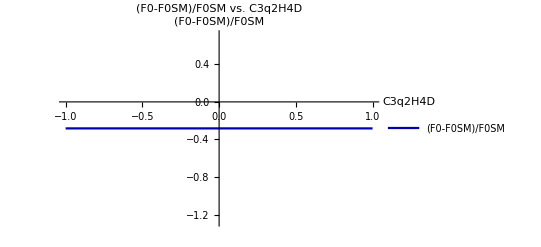

```mathematica
Plot[(F0-F0SM)/F0SM,{C3q2H4D,-1,1},PlotStyle->{Darker[Blue]},AxesLabel->{"C3q2H4D ","(F0-F0SM)/F0SM"},PlotLabel->"(F0-F0SM)/F0SM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"(F0-F0SM)/F0SM"}]
```

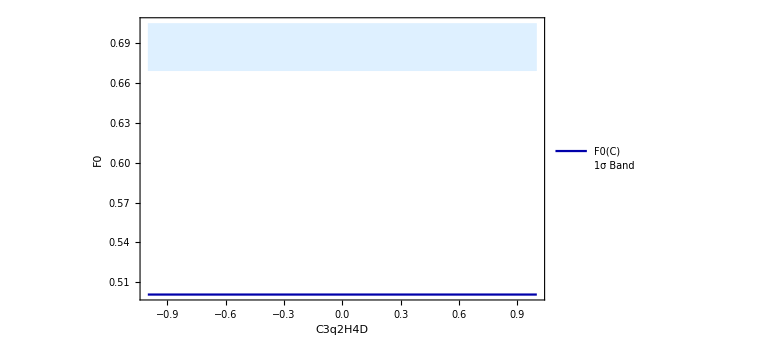

```mathematica
Plot[{F0,F0exp-dF0,F0exp+dF0},{C3q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C3q2H4D","F0"},PlotLegends->{"F0(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C3q2H4D","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
Table[{CudH4D,F0-F0SM},{CudH4D,-1,1,0.2}]
```

(-1. | -0.198873
-0.8 | -0.198507
-0.6 | -0.198141
-0.4 | -0.197776
-0.2 | -0.197412
0. | -0.197049
0.2 | -0.196687
0.4 | -0.196325
0.6 | -0.195965
0.8 | -0.195605
1. | -0.195246)

```mathematica
F0
```

(3.58298×10^9 (1.58026×10^28 (Conjugate[CudH4D])^2-1.77084×10^28 Conjugate[CudH4D]-2.63197×10^13 (0.916835 (-1.4854×10^16 Conjugate[CudH4D]-7.66184×10^17)+8.93724×10^14)-1.00749×10^12 (9.32338×10^17-1.66399×10^18 Conjugate[CudH4D])+6.5926×10^31))/(7.55245×10^15 (-2.52033×10^22 Conjugate[CudH4D]-7.79745×10^23)-3.60982×10^21 (-2.38466×10^18 Conjugate[CudH4D]-5.38178×10^19)+8.67311×10^14 (9.35562×10^22 (Conjugate[CudH4D])^2+4.44228×10^24 Conjugate[CudH4D]+8.60137×10^25)+3.34142×10^41)

```mathematica
F0-F0SM
```

(3.58298×10^9 (1.58026×10^28 (Conjugate[CudH4D])^2-1.77084×10^28 Conjugate[CudH4D]-2.63197×10^13 (0.916835 (-1.4854×10^16 Conjugate[CudH4D]-7.66184×10^17)+8.93724×10^14)-1.00749×10^12 (9.32338×10^17-1.66399×10^18 Conjugate[CudH4D])+6.5926×10^31))/(7.55245×10^15 (-2.52033×10^22 Conjugate[CudH4D]-7.79745×10^23)-3.60982×10^21 (-2.38466×10^18 Conjugate[CudH4D]-5.38178×10^19)+8.67311×10^14 (9.35562×10^22 (Conjugate[CudH4D])^2+4.44228×10^24 Conjugate[CudH4D]+8.60137×10^25)+3.34142×10^41)-0.69779

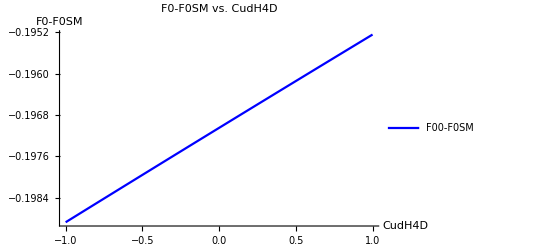

```mathematica
Plot[F0-F0SM,{CudH4D,-1,1},PlotStyle->{Blue},AxesLabel->{"CudH4D ","F0-F0SM"},PlotLabel->"F0-F0SM vs. CudH4D ",PlotRange->All,PlotLegends->{"F00-F0SM"}]
```

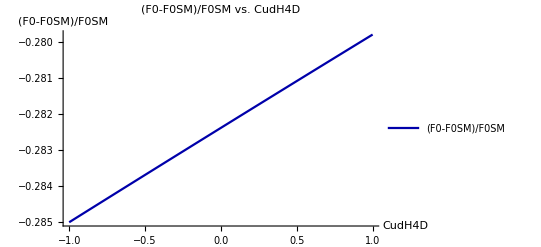

```mathematica
Plot[(F0-F0SM)/F0SM,{CudH4D,-1,1},PlotStyle->{Darker[Blue]},AxesLabel->{"CudH4D ","(F0-F0SM)/F0SM"},PlotLabel->"(F0-F0SM)/F0SM vs. CudH4D ",PlotRange->All,PlotLegends->{"(F0-F0SM)/F0SM"}]
```

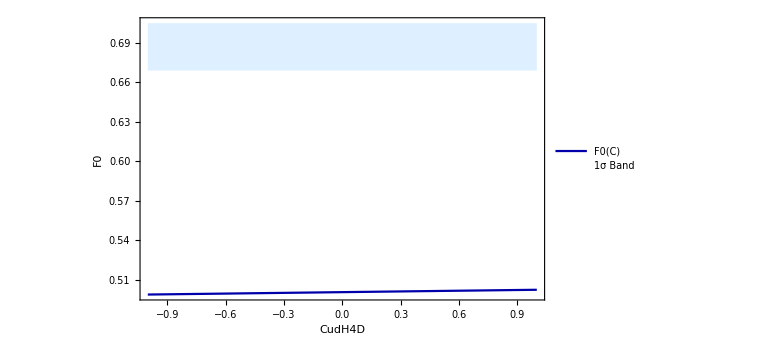

```mathematica
Plot[{F0,F0exp-dF0,F0exp+dF0},{CudH4D,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"CudH4D","F0"},PlotLegends->{"F0(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CudH4D","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

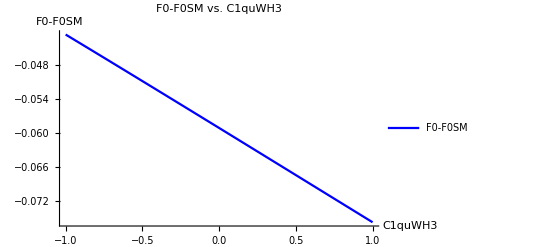

```mathematica
Plot[F0-F0SM,{C1quWH3,-1,1},PlotStyle->{Blue},AxesLabel->{"C1quWH3 ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

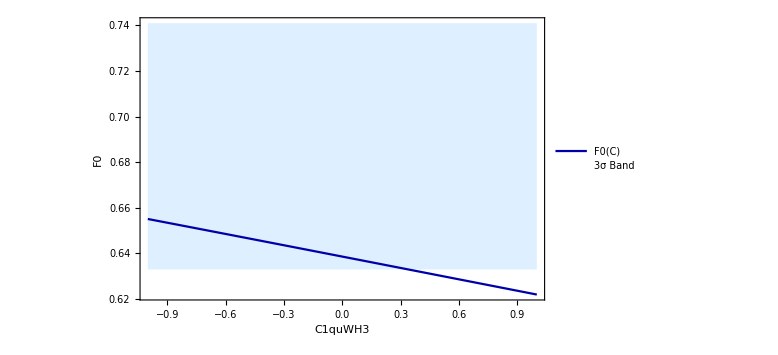

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C1quWH3","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

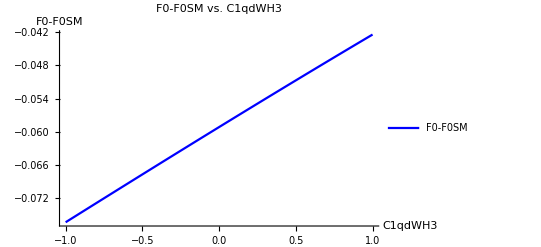

```mathematica
Plot[F0-F0SM,{C1qdWH3,-1,1},PlotStyle->{Blue},AxesLabel->{"C1qdWH3 ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

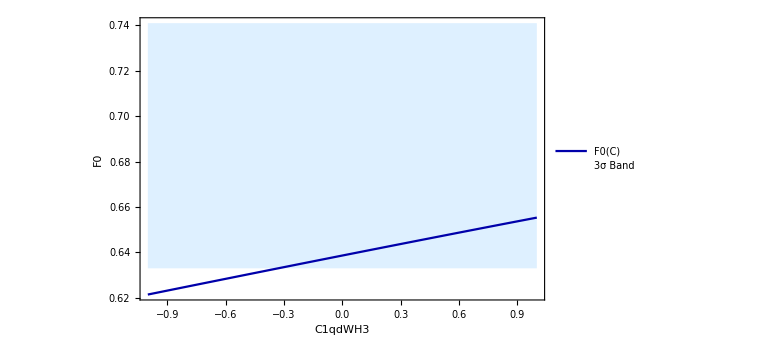

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{C1qdWH3,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C1qdWH3","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1qdWH3","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
F0
```

(3.58298×10^9 (-5.6368×10^18 (-2.48962×10^9 C3q2H4D^2-3.87025×10^8 C3q2H4D Conjugate[C3q2H4D]-7.00865×10^8 (Conjugate[C3q2H4D])^2+3.57751×10^9 C3q2H4D Re(C3q2H4D)+0.)+5.97597×10^12 (0.916835 (173834. (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)+2.5466×10^17)-2.6286×10^14)+3.2563×10^11 (61765.1 (-4.10736×10^11 Re(C3q2H4D)+112.156 (3662186256 C3q2H4D+125000000000)-3.16298×10^11)+0.)+14648745024000000 (7.36422×10^13 (C3q2H4D-Re(C3q2H4D))+0.)-8.65795×10^27 (C3q2H4D-Re(C3q2H4D))+2.28658×10^31))/(-5.43791×10^17 (-0.420293 (13411608173635297536 C3q2H4D^2+3662186256000000000000 C3q2H4D+62500000000000000000000)-25434.4 (221620863468096 (Conjugate[C3q2H4D])^2-443241726936192 C3q2H4D Conjugate[C3q2H4D]-60516000000000000 Re(C3q2H4D))+7.81962×10^18)-8.40043×10^13 (-15284.8 (13411608173635297536 C3q2H4D^2+13411608173635297536 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D])+3662186256000000000000 (C3q2H4D-Re(C3q2H4D))+62500000000000000000000)+3.02509×10^14 (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)-5.68751×10^23)+7.55245×10^15 (4.0655×10^7 (33342.5 (-3662186256 Re(C3q2H4D)+3662186256 C3q2H4D+125000000000)-5.49916×10^13)+0.)+1.16673×10^21 (185295. (-4.10736×10^11 Re(C3q2H4D)+112.156 (3662186256 C3q2H4D+125000000000)-3.16298×10^11)+1.28546×10^19)+2.76956×10^40)

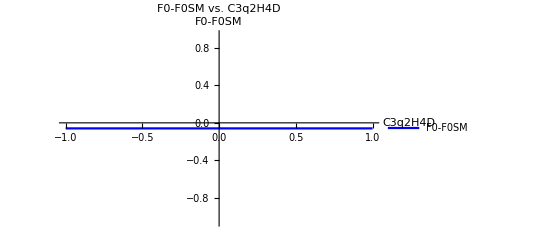

```mathematica
Plot[F0-F0SM,{C3q2H4D,-1,1},PlotStyle->{Blue},AxesLabel->{"C3q2H4D ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

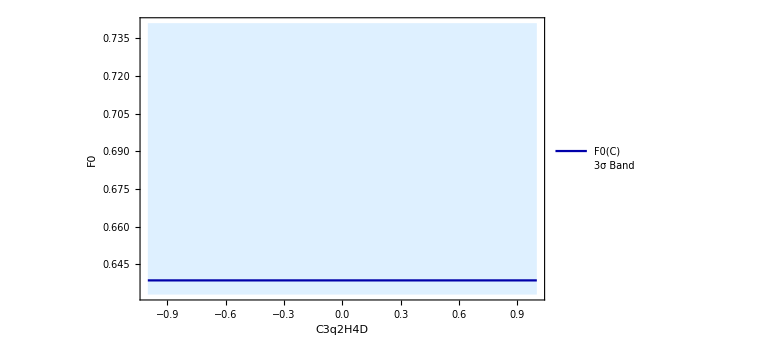

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{C3q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C3q2H4D","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C3q2H4D","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
F0
```

(3.58298×10^9 (-5.6368×10^18 (0.-2.80346×10^9 C2q2H4D^2)+1.58026×10^28 (Conjugate[C2q2H4D])^2+3.16051×10^28 C2q2H4D Conjugate[C2q2H4D]-8.65795×10^27 (Conjugate[C2q2H4D]+C2q2H4D)+14648745024000000 (7.36422×10^13 (Conjugate[C2q2H4D]+C2q2H4D)+0.)+3.2563×10^11 (61765.1 (4.10736×10^11 Conjugate[C2q2H4D]+112.156 (3662186256 C2q2H4D+125000000000)-3.16298×10^11)+0.)+5.97597×10^12 (0.916835 (173834. (3662186256 (Conjugate[C2q2H4D]+C2q2H4D)+125000000000)+2.5466×10^17)-2.6286×10^14)+2.28658×10^31))/(-5.43791×10^17 (-0.420293 (53646432694541190144 C2q2H4D^2+3662186256000000000000 C2q2H4D+62500000000000000000000)-25434.4 (886483453872384 (Conjugate[C2q2H4D])^2+484128 (3662186256 C2q2H4D+125000000000) Conjugate[C2q2H4D])+7.81962×10^18)-8.40043×10^13 (-15284.8 (53646432694541190144 C2q2H4D^2+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+53646432694541190144 (Conjugate[C2q2H4D])^2+3662186256000000000000 (Conjugate[C2q2H4D]+C2q2H4D)+62500000000000000000000)+3.02509×10^14 (3662186256 (Conjugate[C2q2H4D]+C2q2H4D)+125000000000)-5.68751×10^23)+1.16673×10^21 (185295. (4.10736×10^11 Conjugate[C2q2H4D]+112.156 (3662186256 C2q2H4D+125000000000)-3.16298×10^11)+1.28546×10^19)+7.55245×10^15 (4.0655×10^7 (33342.5 (3662186256 (Conjugate[C2q2H4D]+C2q2H4D)+125000000000)-5.49916×10^13)+0.)+2.76956×10^40)

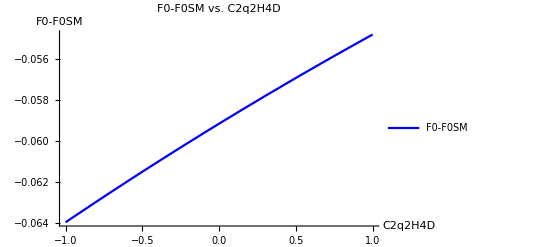

```mathematica
Plot[F0-F0SM,{C2q2H4D,-1,1},PlotStyle->{Blue},AxesLabel->{"C2q2H4D ","F0-F0SM"},PlotLabel->"F0-F0SM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

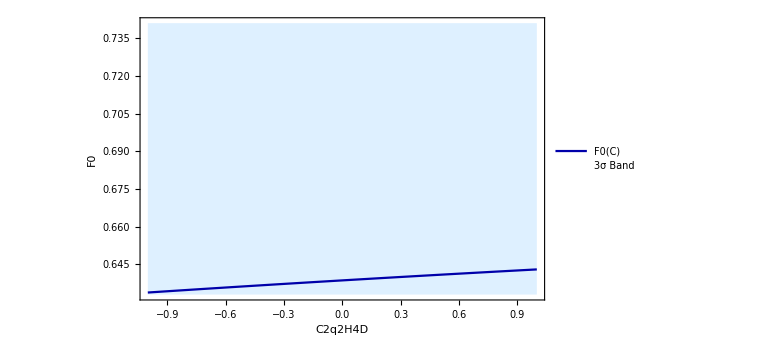

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{C2q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"C2q2H4D","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C2q2H4D","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
F0
```

(3.58298×10^9 (1.58026×10^28 (Conjugate[CudH4D])^2-1.60757×10^28 Conjugate[CudH4D]+5.97597×10^12 (0.916835 (2.7639×10^17-1.4854×10^16 Conjugate[CudH4D])-2.6286×10^14)+3.2563×10^11 (8.46379×10^17-1.66399×10^18 Conjugate[CudH4D])+2.28658×10^31))/(7.55245×10^15 (1.67207×10^23-2.28796×10^22 Conjugate[CudH4D])+1.16673×10^21 (1.53937×10^19-2.38466×10^18 Conjugate[CudH4D])+8.67311×10^14 (9.35562×10^22 (Conjugate[CudH4D])^2-1.00863×10^24 Conjugate[CudH4D]+4.43428×10^24)+1.1525×10^41)

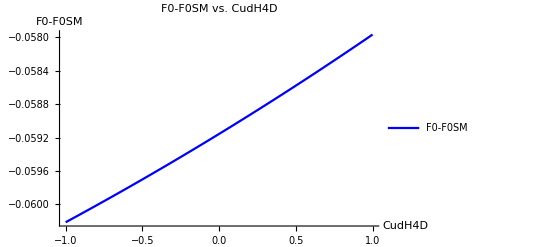

```mathematica
Plot[F0-F0SM,{CudH4D,-1,1},PlotStyle->{Blue},AxesLabel->{"CudH4D ","F0-F0SM"},PlotLabel->"F0-F0SM vs. CudH4D ",PlotRange->All,PlotLegends->{"F0-F0SM"}]
```

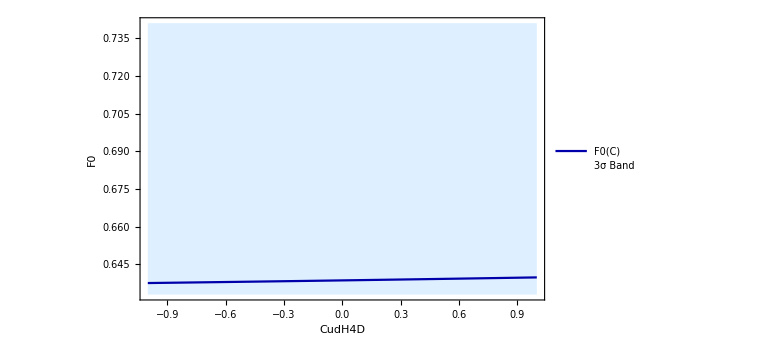

```mathematica
Plot[{F0,F0exp-3*dF0,F0exp+3*dF0},{CudH4D,-1,1},Filling->{2->{3}},FillingStyle->LightBlue,PlotStyle->{Darker[Blue],None,None},PlotRange->All,AxesLabel->{"CudH4D","F0"},PlotLegends->{"F0(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CudH4D","F0"},PlotStyle->{{Thick,Darker[Blue]},{Dashed},{Dashed}}]
```

```mathematica
rho={{1.0,0.0,0.0},{0.0,1.0,-0.87},{0.0,-0.87,1.0}};
sigma={0.014,0.014,0.003};
```

```mathematica
Sigma = Table[sigma[[i]] * rho[[i, j]] * sigma[[j]], {i, 3}, {j, 3}];
SigmaInv = Inverse[Sigma];
```

```mathematica
Chi2[C_]:=Module[{delta},delta=F0-F0exp;
delta SigmaInv delta]
```

SetDelayed::write: Tag List in ((5102.04 (1.27094×10^42+C1quWH3 (4.34815×10^40+Times[«2»]))^2)/((3.20398×10^43+C1quWH3 (1.23124×10^41+Times[«2»]))^2) | 0. | 0.
0. | (20987.4 (1.27094×10^42+C1quWH3 (4.34815×10^40+Times[«2»]))^2)/((3.20398×10^43+C1quWH3 (1.23124×10^41+Times[«2»]))^2) | (85208.9 (1.27094×10^42+C1quWH3 (4.34815×10^40+Times[«2»]))^2)/((3.20398×10^43+C1quWH3 (1.23124×10^41+Times[«2»]))^2)
0. | (85208.9 (1.27094×10^42+C1quWH3 («23»+Times[«2»]))^2)/((3.20398×10^43+C1quWH3 («1»))^2) | (457059. (1.27094×10^42+«1»)^2)/((3.20398×10^43+C1quWH3 («1»))^2))(C_) is Protected.

$Failed

```mathematica
Chi2=Chi2[C1quWH3]//FullSimplify
```

((5102.04 (C1quWH3 (1.48764×10^38 C1quWH3+4.34815×10^40)+1.27094×10^42)^2)/((C1quWH3 (2.55036×10^38 C1quWH3+1.23124×10^41)+3.20398×10^43)^2) | 0. | 0.
0. | (20987.4 (C1quWH3 (1.48764×10^38 C1quWH3+4.34815×10^40)+1.27094×10^42)^2)/((C1quWH3 (2.55036×10^38 C1quWH3+1.23124×10^41)+3.20398×10^43)^2) | (85208.9 (C1quWH3 (1.48764×10^38 C1quWH3+4.34815×10^40)+1.27094×10^42)^2)/((C1quWH3 (2.55036×10^38 C1quWH3+1.23124×10^41)+3.20398×10^43)^2)
0. | (85208.9 (C1quWH3 (1.48764×10^38 C1quWH3+4.34815×10^40)+1.27094×10^42)^2)/((C1quWH3 (2.55036×10^38 C1quWH3+1.23124×10^41)+3.20398×10^43)^2) | (457059. (C1quWH3 (1.48764×10^38 C1quWH3+4.34815×10^40)+1.27094×10^42)^2)/((C1quWH3 (2.55036×10^38 C1quWH3+1.23124×10^41)+3.20398×10^43)^2))(C1quWH3)

```mathematica
F0
```

(2.4916×10^37 C1quWH3^2+4.03661×10^40 C1quWH3+2.05482×10^43)/(2.55036×10^38 C1quWH3^2+1.23124×10^41 C1quWH3+3.20398×10^43)

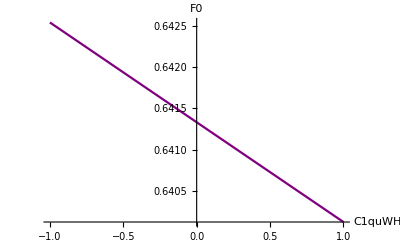

```mathematica
PlotF0=Plot[F0, {C1quWH3, -1, 1}, AxesLabel -> {"C1quWH3", "F0"}, PlotStyle -> {Purple}(*PlotLabel->"F_L vs Wilson Coefficient\

CudH4D"*),PlotRange -> All, PlotStyle -> Thick]
```